```mathematica
a=0;b=4;c=0.001;
```

```mathematica
λ=Table[i,{i,a,b,c}];z0=Table[0.2,{i,a,b,c}];
```

```mathematica
f[x_]:=1.λ*x(1-x)
```

```mathematica
z=f[z0];
```

```mathematica
Table[z=f[z],1000];
```

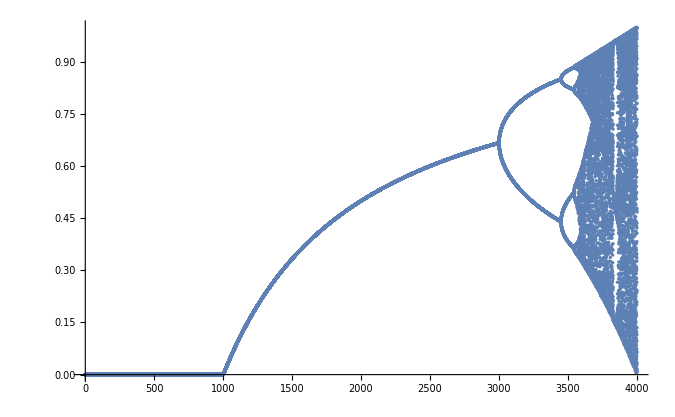

```mathematica
Show[Table[{z=f[z];ListPlot[z]},20]]
```